```mathematica
NN = 100
cc[k_]  :=  Exp[ (ⅈ 2 π k)/NN]
circ= Array[cc, NN, 0];
m[μ_,θ_] := μ ⅇ^(ⅈ θ)
mm[μ_,θ_] = m[μ, θ]  circ;
```

100

```mathematica
σ0[μ_,θ_] := (  1  +  ( - m[μ,θ])^NN )^(1/NN)
σ[z_] := (  1  +  ( - z)^NN )^(1/NN)
eqns[μ_,θ_] := 1/m[μ,θ](  -  1/NN∑_(j=0)^(NN-1) mm[μ,θ][[j+1]] Log [  mm[μ,θ][[j+1]] ] )
eqnsz[ z_ ] := 1/z( -  1/NN∑_(j=0)^(NN-1) z circ[[j+1]] Log [   z circ[[j+1]]   ])
m1 = - ⅇ^(ⅈ π / NN)
eqn[μ_,θ_] := 1/m[μ,θ]( σ0[μ,θ]  -  1/NN∑_(j=0)^(NN-1) mm[μ,θ][[j+1]] Log [ σ0[μ,θ]  +   mm[μ,θ][[j+1]] ] )
eqnz[z_] := 1/z( σ[z]  -  1/NN∑_(j=0)^(NN-1) z circ[[j+1]] Log [ σ[z] + z circ[[j+1]]] )
sumz[z_] := z/Abs[z] 1/NN∑_(j=0)^(NN-1) circ[[j+1]] Log [ σ[z] + z circ[[j+1]]] 
sumz1[z_] := z/Abs[z] 1/NN∑_(j=0)^(NN-1) circ[[j+1]] Log [  z + z circ[[j+1]]]
```

-ⅇ^((ⅈ π)/100)

```mathematica
z = 2.0 Exp[ ⅈ 0.7]; sumz[z]
```

0.315767-0.0187058 ⅈ

```mathematica
σ[z]
```

1.99992+0.017699 ⅈ

```mathematica
eqnz[m1] // N
```

-0.998684+0.0628319 ⅈ

```mathematica
FindRoot[ Re[eqn[μ,0.7]] == 0, {μ, 1.5} ]
```

{μ→3.88892}

```mathematica
FindRoot[Re[ eqnz[z]] == 0, {z, ⅇ^(ⅈ 0.4)} ]
```

{z→12.3238+0.389418 ⅈ}

```mathematica
MMM = 500
```

500

```mathematica
radii = Table[ {Null,Null}, {MMM}];
radiiN = Table[ {Null,Null}, {MMM}];
radiiNconj = Table[ {Null,Null}, {MMM}];
radiiz = Table[ {Null,Null}, {MMM}];
```

```mathematica
dθ = (π / NN)/MMM;
```

```mathematica
For [ k = 0, k < MMM, k++, 
          rad = μ /. FindRoot[  Re[eqn[μ, k dθ ]] == 0, {μ, 1.0} ] // N;
(*
radz = z /. FindRoot[ Re[eqnz[z]] == 0, {z, ⅇ^(ⅈ  k dθ) } ] // N;
*)

radii[[ k + 1 ]] = { rad Cos [ k dθ ], rad Sin [ k dθ ] };
radiiN[[ k + 1 ]] = { rad^NN Cos [ NN k dθ ], rad^NN Sin [ NN k dθ ] };
radiiNconj[[k+1]] = { radiiN[[k+1]][[1]], -radiiN[[k+1]][[2]] }
(*
radiiz[[ k + 1]] = { Re[radz^NN], Im[radz^NN] };
*)
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

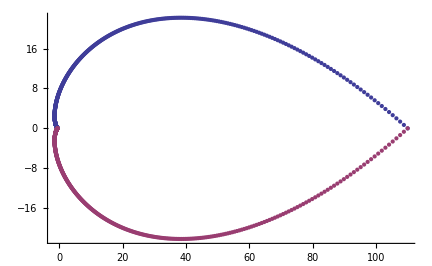

```mathematica
ListPlot[{radiiN,radiiNconj} ⅇ^-NN]
```